Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# Práctica 3. Sucesiones de números reales

## Ejemplos

## Definir una sucesión Evaluar o calcular algunos términos Representar algunos términos Calcular el limite de una sucesión Aceleración de la convergencia Método de Montecarlo Definición de sucesiones por recurrencia

Podemos definir una sucesión, como definiríamos una función:

```mathematica
a[n_]:= √((n+1)/n)
```

Una vez definida, podemos evaluar, o calcular, un término de la sucesión

```mathematica
a[3]
```

2/(√3)

Para evaluar varios términos de la sucesión construimos una lista.

```mathematica
{a[3], a[5],a[8]}
```

{2/(√3),√(6/5),3/(2 √2)}

Para conocer los valores aproximados podemos añadir //N

```mathematica
{a[3], a[5],a[8], a[20]}//N
```

{1.1547,1.09545,1.06066,1.0247}

Al evaluar vemos como los valores parecen ir descendiendo y acercarse al 1. También podemos representar algunos términos de la sucesión con la función DiscretePlot.
Observemos que es una palabra compuesta, por ello escribimos en mayúscula la inicial de cada palabra, el resto se escribe en minúsculas.

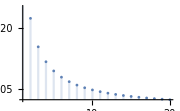

```mathematica
DiscretePlot[a[n],{n,1,20}]
```

El Mathematica también puede calcular el límite de una sucesión.

```mathematica
Limit[a[n],n->∞]
```

1

Para escribir “la flecha” y el símbolo del infinito, podemos utilizar la paleta y buscarlos en la fila donde están los números 1, 2, 3. A la derecha están la flecha “→” y el símbolo “∞”. La flecha también puede escribirse con el menos y el mayor; - > (al seguir escribiendo se combinan y forman la flecha). Respecto al Infinito también puede escribirse como Infinity.

En ocasiones, el límite de podría no existir para valores cualesquiera de n. En nuestro caso, nos interesa para valores de n que sean números naturales. Por tanto, podríamos utilizar una nueva instrucción, DiscretePlot, donde la expresión es evaluada solo en números naturales. Por ejemplo,

```mathematica
Limit[Cos[2π n],n->∞]
```

Indeterminate

```mathematica
DiscreteLimit[Cos[2π n],n->∞]
```

1

La función coseno de 2π x no tiene límite en infinito, sin embargo, si evaluamos en números naturales, la sucesión que obtenemos es la constantemente 1.


Si en alguna ocasión el Mathematica no pudiese calcular el límite, podríamos pensar que con evaluar o calcular un término bastante avanzado de la sucesión bastaría para conocer el límite. Esto podría ser admisible si la sucesión se “acercase” al límite bastante rápidamente.

```mathematica
b[n_]:= n^2/2^n
```

```mathematica
{b[10],b[100],b[1000]}//N
```

{0.0976563,7.88861×10^-27,9.33264×10^-296}

En este caso, el límite parece que va a ser cero

```mathematica
Limit[b[n],n->∞]
```

0

Sin embargo, hay sucesiones que convergen de forma “muy lenta”.

#### Aceleración de la convergencia

Un ejemplo de sucesión que converge lentamente es la sucesión de Leibniz para el cálculo del número π.

```mathematica
c[n_]:=4 ∑_(i=0)^n (-1)^i/(2i+1)
```

```mathematica
{c[10],c[100],c[1000]}//N
```

{3.23232,3.15149,3.14259}

Habría que avanzar mucho en la sucesión para conseguir unas cuantas cifras decimales exactas del número π.
Una posibilidad es utilizar alguna técnica de aceleración de la convergencia.

Una de las técnicas de aceleración de la convergencia es la del Δ^2 de Aitken.

Supongamos que en cada paso el error (diferencia entre el término de la sucesión y el límite) se redujese en una cierta proporción. Entonces,
			(x_(n+1)- L)/(x_n- L) = (x_(n+2)- L)/(x_(n+1)- L)
Despejando L,
			L = (x_nx_(n+2)-x_(n+1)x_(n+1))/(x_(n+2)-2x_(n+1)+x_n)= x_(n+2) -  (x_(n+2)-x_(n+1))^2 / (x_(n+2)-2x_(n+1)+x_n)
			
En general, las sucesiones no tienen que cumplir esta condición, y por tanto, no podríamos calcular L de esa forma, pero se podría crear una nueva sucesión

			 y_n = x_(n+2) -  (x_(n+2)-x_(n+1))^2 / (x_(n+2)-2x_(n+1)+x_n)
			 
que en ciertas circunstancias podría acercarse al límite de forma más rápida que la sucesión original.

```mathematica
d[n_]:=c[n+2]-(c[n+2]-c[n+1])^2/(c[n+2]-2c[n+1]+c[n])
```

Calculemos algunos términos de la nueva sucesión (comparamos la sucesión original, la sucesión “acelerada” y el límite)

```mathematica
MatrixForm[Table[N[{n,c[n],d[n],Pi},10],{n,1,30}]]
```

(1. | 2.666666667 | 3.133333333 | 3.141592654
2. | 3.466666667 | 3.145238095 | 3.141592654
3. | 2.895238095 | 3.13968254 | 3.141592654
4. | 3.33968254 | 3.142712843 | 3.141592654
5. | 2.976046176 | 3.140881341 | 3.141592654
6. | 3.283738484 | 3.142071817 | 3.141592654
7. | 3.017071817 | 3.141254824 | 3.141592654
8. | 3.252365935 | 3.141839619 | 3.141592654
9. | 3.041839619 | 3.141406718 | 3.141592654
10. | 3.232315809 | 3.141736099 | 3.141592654
11. | 3.058402766 | 3.141479689 | 3.141592654
12. | 3.218402766 | 3.141683189 | 3.141592654
13. | 3.070254618 | 3.141518986 | 3.141592654
14. | 3.208185652 | 3.141653394 | 3.141592654
15. | 3.079153394 | 3.141541986 | 3.141592654
16. | 3.200365515 | 3.141635357 | 3.141592654
17. | 3.086079801 | 3.14155633 | 3.141592654
18. | 3.194187909 | 3.141623807 | 3.141592654
19. | 3.091623807 | 3.141565735 | 3.141592654
20. | 3.189184782 | 3.141616072 | 3.141592654
21. | 3.096161526 | 3.141572154 | 3.141592654
22. | 3.185050415 | 3.141610699 | 3.141592654
23. | 3.099944032 | 3.141576685 | 3.141592654
24. | 3.181576685 | 3.141606851 | 3.141592654
25. | 3.103145313 | 3.141579974 | 3.141592654
26. | 3.178617011 | 3.141604024 | 3.141592654
27. | 3.105889738 | 3.141582418 | 3.141592654
28. | 3.176065177 | 3.1416019 | 3.141592654
29. | 3.108268567 | 3.141584273 | 3.141592654
30. | 3.173842337 | 3.141600274 | 3.141592654)

Observamos que el primer decimal queda fijo para la sucesión inicial a partir del término 24, pero que en la segunda se consigue desde el primer término o que fija los tres primeros decimales desde el séptimo término.

Podemos ver el comportamiento en términos más avanzados:

```mathematica
MatrixForm[Table[N[{n,c[n],d[n],Pi},10],{n,101,130}]]
```

(101. | 3.131788968 | 3.141592425 | 3.141592654
102. | 3.151301163 | 3.141592876 | 3.141592654
103. | 3.131977491 | 3.141592438 | 3.141592654
104. | 3.151116247 | 3.141592863 | 3.141592654
105. | 3.132158901 | 3.14159245 | 3.141592654
106. | 3.150938244 | 3.141592852 | 3.141592654
107. | 3.132333593 | 3.141592461 | 3.141592654
108. | 3.150766772 | 3.141592841 | 3.141592654
109. | 3.132501932 | 3.141592471 | 3.141592654
110. | 3.15060148 | 3.141592832 | 3.141592654
111. | 3.13266426 | 3.14159248 | 3.141592654
112. | 3.150442038 | 3.141592822 | 3.141592654
113. | 3.132820892 | 3.141592489 | 3.141592654
114. | 3.150288141 | 3.141592814 | 3.141592654
115. | 3.132972124 | 3.141592498 | 3.141592654
116. | 3.150139506 | 3.141592806 | 3.141592654
117. | 3.133118229 | 3.141592505 | 3.141592654
118. | 3.149995867 | 3.141592798 | 3.141592654
119. | 3.133259465 | 3.141592512 | 3.141592654
120. | 3.149856975 | 3.141592791 | 3.141592654
121. | 3.13339607 | 3.141592519 | 3.141592654
122. | 3.149722601 | 3.141592785 | 3.141592654
123. | 3.133528269 | 3.141592526 | 3.141592654
124. | 3.149592526 | 3.141592779 | 3.141592654
125. | 3.133656271 | 3.141592532 | 3.141592654
126. | 3.149466547 | 3.141592773 | 3.141592654
127. | 3.133780273 | 3.141592537 | 3.141592654
128. | 3.149344475 | 3.141592767 | 3.141592654
129. | 3.13390046 | 3.141592542 | 3.141592654
130. | 3.14922613 | 3.141592762 | 3.141592654)

Para el término 130 la primera sucesión aún no ha fijado el segundo decimal, sin embargo, la sucesión “acelerada” ya ha fijado seis decimales.

```mathematica
MatrixForm[Table[N[{n,c[n],d[n],Pi},12],{n,1000,1030}]]
```

(1000. | 3.14259165434 | 3.14159265384 | 3.14159265359
1001. | 3.14059464985 | 3.14159265334 | 3.14159265359
1002. | 3.14258966232 | 3.14159265384 | 3.14159265359
1003. | 3.1405966379 | 3.14159265334 | 3.14159265359
1004. | 3.14258767822 | 3.14159265384 | 3.14159265359
1005. | 3.14059861805 | 3.14159265334 | 3.14159265359
1006. | 3.142585702 | 3.14159265383 | 3.14159265359
1007. | 3.14060059034 | 3.14159265335 | 3.14159265359
1008. | 3.14258373362 | 3.14159265383 | 3.14159265359
1009. | 3.14060255482 | 3.14159265335 | 3.14159265359
1010. | 3.14258177303 | 3.14159265383 | 3.14159265359
1011. | 3.14060451154 | 3.14159265335 | 3.14159265359
1012. | 3.14257982018 | 3.14159265383 | 3.14159265359
1013. | 3.14060646054 | 3.14159265335 | 3.14159265359
1014. | 3.14257787503 | 3.14159265383 | 3.14159265359
1015. | 3.14060840186 | 3.14159265335 | 3.14159265359
1016. | 3.14257593752 | 3.14159265383 | 3.14159265359
1017. | 3.14061033556 | 3.14159265335 | 3.14159265359
1018. | 3.14257400762 | 3.14159265383 | 3.14159265359
1019. | 3.14061226167 | 3.14159265335 | 3.14159265359
1020. | 3.14257208528 | 3.14159265382 | 3.14159265359
1021. | 3.14061418024 | 3.14159265336 | 3.14159265359
1022. | 3.14257017046 | 3.14159265382 | 3.14159265359
1023. | 3.14061609132 | 3.14159265336 | 3.14159265359
1024. | 3.14256826311 | 3.14159265382 | 3.14159265359
1025. | 3.14061799495 | 3.14159265336 | 3.14159265359
1026. | 3.14256636319 | 3.14159265382 | 3.14159265359
1027. | 3.14061989117 | 3.14159265336 | 3.14159265359
1028. | 3.14256447066 | 3.14159265382 | 3.14159265359
1029. | 3.14062178003 | 3.14159265336 | 3.14159265359
1030. | 3.14256258547 | 3.14159265382 | 3.14159265359)

Para el término 1030 la primera sucesión solo tiene 2 decimales exactos, sin embargo, la sucesión “acelerada” ya ha fijado nueve decimales.

```mathematica
Limit[d[n],n->∞]
```

π

La nueva sucesión tiene el mismo límite, pero converge de forma más rápida y muchos decimales se obtienen mucho antes.

Podríamos también en pensar en “acelerar” la sucesión “acelerada”. Es decir, de la sucesión {c_n} hemos construido la sucesión {d_n} y de esta última podríamos crear otra sucesión {e_n} siguiendo la misma fórmula:

```mathematica
e[n_]:=d[n+2]-(d[n+2]-d[n+1])^2/(d[n+2]-2d[n+1]+d[n])
```

```mathematica
MatrixForm[Table[N[{n,c[n],d[n],e[n],Pi},12],{n,1,30}]]
```

(1. | 2.66666666667 | 3.13333333333 | 3.14145021645 | 3.14159265359
2. | 3.46666666667 | 3.14523809524 | 3.141643324 | 3.14159265359
3. | 2.89523809524 | 3.13968253968 | 3.1415712902 | 3.14159265359
4. | 3.33968253968 | 3.14271284271 | 3.1416028416 | 3.14159265359
5. | 2.97604617605 | 3.14088134088 | 3.14158732095 | 3.14159265359
6. | 3.28373848374 | 3.14207181707 | 3.14159565524 | 3.14159265359
7. | 3.01707181707 | 3.14125482361 | 3.14159086271 | 3.14159265359
8. | 3.25236593472 | 3.14183961893 | 3.14159377424 | 3.14159265359
9. | 3.04183961893 | 3.1414067185 | 3.14159192394 | 3.14159265359
10. | 3.23231580941 | 3.14173609926 | 3.14159314487 | 3.14159265359
11. | 3.05840276593 | 3.141479689 | 3.14159231316 | 3.14159265359
12. | 3.21840276593 | 3.14168318921 | 3.14159289543 | 3.14159265359
13. | 3.07025461778 | 3.1415189856 | 3.14159247802 | 3.14159265359
14. | 3.20818565226 | 3.1416533942 | 3.14159278352 | 3.14159265359
15. | 3.0791533942 | 3.141541986 | 3.14159255579 | 3.14159265359
16. | 3.20036551541 | 3.14163535668 | 3.14159272833 | 3.14159265359
17. | 3.08607980112 | 3.14155633028 | 3.14159259568 | 3.14159265359
18. | 3.19418790923 | 3.14162380667 | 3.14159269901 | 3.14159265359
19. | 3.09162380667 | 3.14156573466 | 3.14159261756 | 3.14159265359
20. | 3.18918478228 | 3.14161607192 | 3.14159268246 | 3.14159265359
21. | 3.09616152646 | 3.14157215448 | 3.14159263023 | 3.14159265359
22. | 3.18505041535 | 3.14161069904 | 3.14159267265 | 3.14159265359
23. | 3.09994403237 | 3.14157668544 | 3.14159263792 | 3.14159265359
24. | 3.18157668544 | 3.14160685135 | 3.14159266657 | 3.14159265359
25. | 3.10314531289 | 3.14157997396 | 3.14159264276 | 3.14159265359
26. | 3.178617011 | 3.14160402399 | 3.14159266268 | 3.14159265359
27. | 3.10588973827 | 3.14158241825 | 3.14159264591 | 3.14159265359
28. | 3.17606517687 | 3.14160190003 | 3.14159266011 | 3.14159265359
29. | 3.1082685667 | 3.14158427267 | 3.14159264803 | 3.14159265359
30. | 3.17384233719 | 3.1416002737 | 3.14159265836 | 3.14159265359)

Observamos que la nueva sucesión parece mejorar aún más la aproximación al límite.

#### Método de Montecarlo

En ocasiones para calcular un área o un volumen nos encontramos que necesitamos calcular integrales complejas, o que tenemos que dividir el recinto de una forma complicada, etc. Una idea sería generar puntos aleatorios e ir comprobando si cada uno está dentro o fuera de la región que queremos calcular. La proporción de puntos tenderá a la proporción que el recinto representa en la región. Este es el método de Montecarlo, el nombre hace referencia al conocido casino.

Por ejemplo, si quisiéramos calcular el área del circulo de radio 1 centrado en el punto (0,0), podríamos generar puntos aleatorios del cuadrado [-1,1]x[-1,1] ( que tiene área 4). Un punto (x_i,y_i) está dentro del círculo si x_i^2+y_i^2≤1. En otro caso estaría fuera. La proporción de puntos que quedan dentro se acercará a la proporción del área del circulo frente al área del cuadrado.

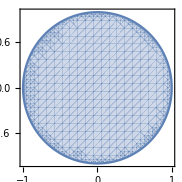

```mathematica
RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]
```

```mathematica
nn=10000
```

10000

```mathematica
puntos=RandomReal[{-1,1},{nn,2}];
```

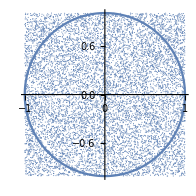

```mathematica
Show[ListPlot[puntos],ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],AspectRatio->Automatic]
```

Vemos como hay puntos dentro y fuera del círculo. Vamos a contar cuántos quedan dentro y obtendremos la proporción que representa el círculo con respecto al área del cuadrado.

```mathematica
dentro=0;
For[i=1,i≤nn,i++,If[ puntos[[i,1]]^2+puntos[[i,2]]^2≤1,dentro=dentro+1];x[i]=4.dentro/i]
```

```mathematica
x[10000]
```

3.14

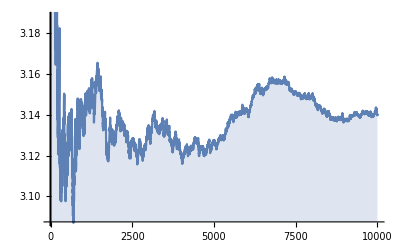

```mathematica
DiscretePlot[x[i],{i,1,nn}]
```

La sucesión x[i] debería aproximar el área del círculo, que sería π.

Veamos otro ejemplo para calcular un volumen. Se trataría de aproximar el volumen de la región  x^2+y^4+ z*Cos[z^2] ≤ 1 con z entre -2 y 2,

```mathematica
RegionPlot3D[x^2+y^4+ z*Cos[z^2] ≤1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
nn=100000
```

100000

```mathematica
puntos=RandomReal[{-2,2},{nn,3}];
```

```mathematica
dentro=0;
For[i=1,i≤nn,i++,If[ puntos[[i,1]]^2+puntos[[i,2]]^4 + puntos[[i,3] ]Cos[puntos[[i,3]]^2]≤1,dentro=dentro+1];x[i]=64.dentro/i]
```

```mathematica
x[100000]
```

13.7037

```mathematica
DiscretePlot[x[i],{i,1,nn}]
```

-Graphics-

La sucesión x[i] debería aproximar el volumen del objeto, que podría estar próximo a 13,7 (aunque cada vez que generemos los puntos podemos encontrar unos valores diferentes).

#### Sucesiones definidas por recurrencia

En ocasiones las sucesiones vienen dada por una recurrencia, de forma que a partir de los primeros términos vamos construyendo los siguientes términos. La sucesión de Fibonacci o la del método babilonio para calcular las raíces cuadradas serían ejemplos de esto.

Supongamos que queremos calcular la raíz cuadrada de 7. A partir de un valor cualquiera, generamos una sucesión calculando el valor medio entre x_i y 7/x_i. 

Por ejemplo, si comenzamos con x_1=1,

```mathematica
Clear[x,i]
```

```mathematica
x[1]=1
```

1

```mathematica
For[i=2,i≤20,i++,x[i]=(x[i-1]+7/x[i-1])/2]
```

Para ver algunos términos de la sucesión podemos formar una lista con algunos términos:

```mathematica
Table[x[i],{i,1,7}]
```

{1,4,23/8,977/368,1902497/719072,7238946623297/2736064645568,104804696428033056657448577/39612451854313553433195392}

```mathematica
N[x[5],20]
```

2.6457670441902897067

```mathematica
MatrixForm[Table[{i,N [x[i],40],N[x[i]-Sqrt[7],40]},{i,1,8}]]
```

(1 | 1. | -1.64575131106459059050161575363926042571
2 | 4. | 1.35424868893540940949838424636073957429
3 | 2.875 | 0.2292486889354094094983842463607395742897
4 | 2.654891304347826086956521739130434782609 | 0.009139993283235496454905985491174356898436
5 | 2.645767044190289706733122691469004494682 | 0.00001573312569911623150693782974406897177544
6 | 2.645751311111369320474788060415261270877 | 4.677872997317230677600084516666909144737×10^-11
7 | 2.64575131106459059050202929393851549386 | 4.135402992550681496741018282024769058051×10^-22
8 | 2.64575131106459059050161575363926042571 | 3.231890661695609461284154951155550862617×10^-44)

El orden de convergencia de una sucesión nos indica cómo se acercan los términos al límite. El método para obtener la raíz cuadrada de los babilonios tiene orden de convergencia cuadrática. Esto significa que Lim_(n → ∞) (|x_(n+1)-L|)/(|x_n-L|^2) = α >0, o dicho de otra forma, el error en el paso n+1, |x_(n+1)-L|, se acerca al error del paso n elevado al cuadrado por una constante. α |x_n-L|^2. 

Observamos en la matriz anterior cómo el error en el paso 6 es del orden de  10^-11 , en el paso 7 de 10^-22, y en el paso 8 de 10^-44. Prácticamente el error en cada uno de estos pasos es el cuadrado del anterior. La convergencia es muy rápida.

Cuidado al efectuar los cálculos. Si trabajamos con números enteros, las fracciones correspondientes a x[i] podrían tener cada vez más cifras y precisar de mucha memoria,

```mathematica
x[12]
```

4203137293672018632502920508511982048799691159569074892048064545457620799002264492014792544188108686934591610931433105280250947560455574395725156314686362632310347276842824756811252610119845453308725472294361524553276115552850749356115915479790192884914567942059053806008187255883764433184823637091914857644416310543870169033334883216495400302073693980145660628217169540658544718136684305989941348882517343622495257091603763573480747889490070404578650636592157220593527979095925029376942104259016325125863633319192860140222606005786683083683058078734540464228604022095273381198432434281283428692067472401402907011215922006992161497872586653479766284990942701495664207322698686475035110248602251497353242945049480401690958963155643799325414519344867600004882403847885063207028602699777/2972066882613557621852541925169138323309787826628766342343560143750851872053152830191140534338291337391539918868852654817529197208774008161652414729892895651445216888435804106584071036958349447235291365729921247453546675586940537298554850148392773327747419329246737962793003941866937488060566997852021985412063466612228622543746105080658504147292055380146378239189636553727043660794873200191133237870795813749065362985638879038663516864114589288118400335478413325207300366411810708866176846876122753459232294161949791542137735182120952319692519928287235107083638029673296238126703073697347755042892087924192351605933524944587595544946127107671877057108182387350711932900873629937227546925022785538701856603767219186802365055374113204670357132684125812560752440492220322084152312567808

Otro ejemplo de sucesión definida por recurrencia.
Construcción de términos de la sucesión de Fibonacci. Partiendo de dos números (originalmente el 1 y el 1), se construye una sucesión donde cada término es la suma de los dos anteriores.

```mathematica
z[1]=1;
```

```mathematica
z[2]=1;
```

```mathematica
For[i=3,i<200,i++,z[i]=z[i-1]+z[i-2]]
```

```mathematica
Table[z[i],{i,1,50}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025}